```mathematica
SetDirectory[NotebookDirectory[EvaluationNotebook[]]];
Needs["NumericalCalculus`"]
```

Note que os parâmetros são inseridos como frações, ou seja, números exatos. Durante esse projeto, eu descobri que isso é muito importante para evitar erros de arredondamento. (Ver análise abaixo.)

```mathematica
Nc=3;
Nf=3; (* UDS com mesma massa. *)
M3=196/1000;
m2=639/1000;
MPrime=14/1000;
conversaoGeV4Mevfm3 = 1.30142*^5; (*1 MeV = (197 fm)^-1*)
```

```mathematica
Omega2[ζ_,p_,mp_]:=p^2+(M3/(-ζ+p^2+m2)+mp)^2
PressureZeroT[mu_,mp_]:=NIntegrate[(1/π^3*Nc*Nf)*(Log[Abs[(Omega2[(ⅈ*θ+mu)^2,p,mp]-(ⅈ*θ+mu)^2)/(Omega2[-θ^2,p,mp]+θ^2)]]*p^2),{θ,0,Infinity},{p,0,mu},MaxRecursion->40,WorkingPrecision->40,AccuracyGoal->12,PrecisionGoal->12,Method->{GlobalAdaptive,MaxErrorIncreases->10000}]
```

Cálculo da pressão desde mu=0.01GeV até mu=1.5GeV

```mathematica
tablePressureZeroT=conversaoGeV4Mevfm3*Table[{mu,PressureZeroT[mu,MPrime]},{mu,0.01`40,2.51`40,0.10`40}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

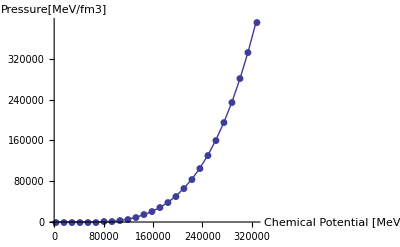

```mathematica
pPressureZeroT=ListLinePlot[tablePressureZeroT,PlotStyle->PointSize[0.01],Joined-> True,PlotMarkers->Automatic,AxesLabel->{"Chemical Potential [MeV]","Pressure[MeV/fm3]"},ImageSize->Full]
```

Fit

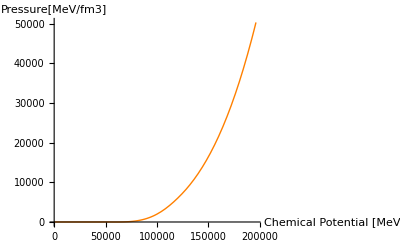

```mathematica
pressao=Interpolation[tablePressureZeroT,Method->"Spline"];
pPressureZeroTInterpolated = Plot[pressao[μ],{μ,0.01,1.51*conversaoGeV4Mevfm3},ImageSize->Full,AxesLabel->{"Chemical Potential [MeV]","Pressure[MeV/fm3]"}, PlotStyle->{Orange, Thick}]
```

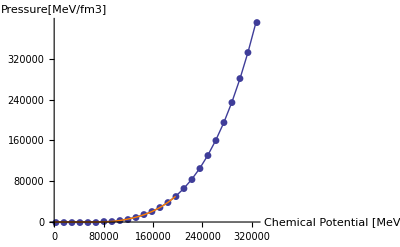

```mathematica
Show[pPressureZeroT, pPressureZeroTInterpolated]
```

Densidade Bariônica Interpolada

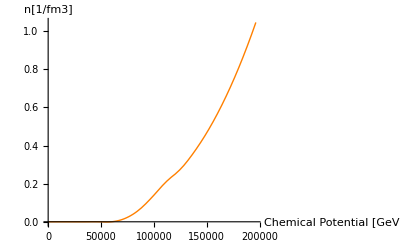

```mathematica
Subscript[n, B] := pressao'
pNb=Plot[Subscript[n, B][μ],{μ,0.01,1.51*conversaoGeV4Mevfm3},PlotStyle->{Orange, Thick},ImageSize->Full,AxesLabel->{"Chemical Potential [GeV]","n[1/fm3]"}]
```

Densidade de Energia

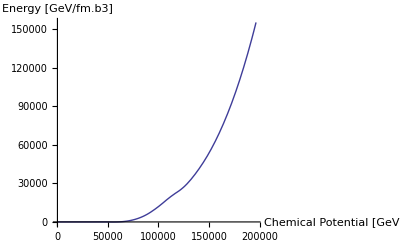

```mathematica
ϵ[μ_] = -pressao[μ]+μ*Subscript[n, B][μ];
pEpsilon=Plot[ϵ[μ],{μ,0.01,1.51*conversaoGeV4Mevfm3},ImageSize->Full,AxesLabel->{"Chemical Potential [GeV]","Energy [GeV/fm.b3]"}]
(*Show[pNb, pEpsilon]*)
```

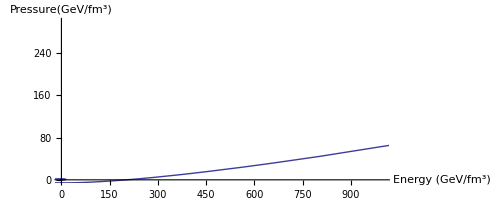

```mathematica
ParametricPlot[{ϵ[μ],pressao[μ]}, {μ,0.01,1.51*conversaoGeV4Mevfm3},ImageSize->Full,PlotRange->{{0,1000},{0,300}}, AxesLabel->{"Energy (GeV/fm^3)","Pressure(GeV/fm^3)"}]
```

```mathematica
tableEoSZeroT=Table[{ϵ[μ],pressao[μ],Subscript[n, B][μ], μ},{μ,0.01,150000,50}];
Export["qcd.ire.eos.CALCTESE_2.dat",tableEoSZeroT];
```